NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.0027349-0.00213817 ⅈ and 0.0252537 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 0.00273781-0.00294296 ⅈ and 0.0356069 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 3.288×10^-6-0.00152065 ⅈ and 0.0503659 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{ϕ[0]→-1862.28-2625.35 ⅈ,ϕ[1]→-2.61283×10^16-1.61086 ⅈ,A[-2]→-44373.9-245350. ⅈ,A[-1]→13952.6+117228. ⅈ,A[1]→1505.7-635.797 ⅈ,A[2]→352.144+253.653 ⅈ,B[-2]→-124.092+64.3929 ⅈ,B[-1]→368.873-2686.37 ⅈ,B[1]→-3796.38+2023.03 ⅈ,B[2]→-130209.-356557. ⅈ}}

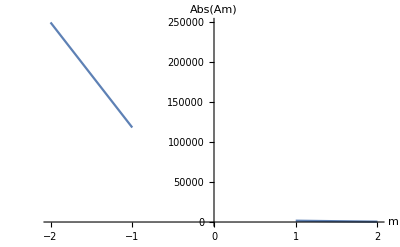

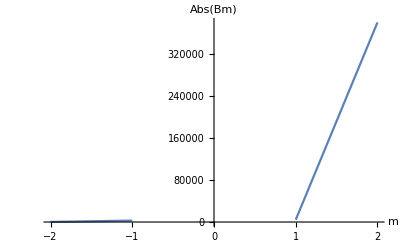

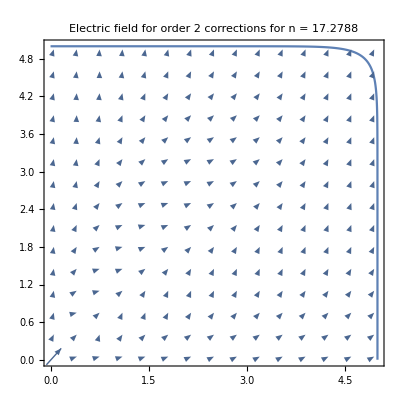

```mathematica
Block[
{M,kMax,m,k,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=2;(* Half the number of coefficients Am or Bm *)
n=N[11π/2];(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia=<||>;Ib=<||>;Ic=<||>;Id=<||>;Ie=<||>;
For[
m=-M,m≤M,m++,
For[
k=1,k≤2M,k++,
Ia=Append[Ia,{m,k}-> NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ib=Append[Ib,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
];
For[
k=0,k≤2M+1,k++,
Ic=Append[Ic,k-> NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Id=Append[Id,{m,k}->NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ie=Append[Ie,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
]
];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[{m,k}]+m B[m]/R^(m+1) Ib[{m,k}],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[{m,k}]+B[m]/R^m Ie[{m,k}],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=Solve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Am)"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Bm)"}]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 3.59895×10^-6-0.00183558 ⅈ and 0.0269853 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 0.000200234-0.00136257 ⅈ and 0.0229286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -1.62302×10^-6-0.0000406855 ⅈ and 0.026915 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{ϕ[0]→3874.54-3657.84 ⅈ,ϕ[1]→-2.61283×10^16+2.02622 ⅈ,A[-3]→-101357.-72125.6 ⅈ,A[-2]→293175.+56496.2 ⅈ,A[-1]→3116.96+20563. ⅈ,A[1]→-713.614-347.509 ⅈ,A[2]→-94.6987-470.772 ⅈ,A[3]→32.4248+28.1432 ⅈ,B[-3]→-24.6256-18.0851 ⅈ,B[-2]→-377.187+113.958 ⅈ,B[-1]→1005.68-81.0046 ⅈ,B[1]→-33532.-22861.1 ⅈ,B[2]→255859.+130399. ⅈ,B[3]→-625774.-1.13377×10^6 ⅈ}}

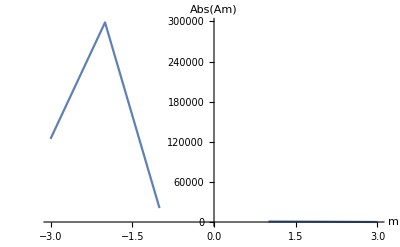

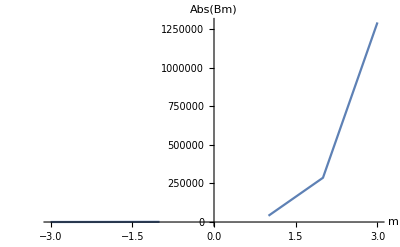

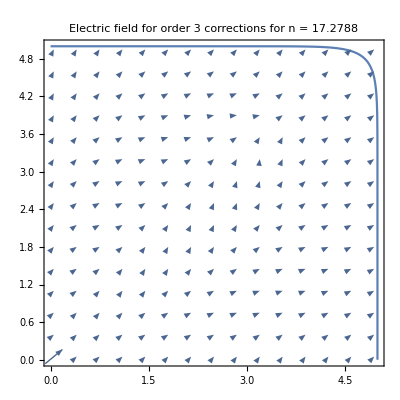

```mathematica
Block[
{M,kMax,m,k,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=3;(* Half the number of coefficients Am or Bm *)
n=N[11π/2];(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia=<||>;Ib=<||>;Ic=<||>;Id=<||>;Ie=<||>;
For[
m=-M,m≤M,m++,
For[
k=1,k≤2M,k++,
Ia=Append[Ia,{m,k}-> NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ib=Append[Ib,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
];
For[
k=0,k≤2M+1,k++,
Ic=Append[Ic,k-> NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Id=Append[Id,{m,k}->NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ie=Append[Ie,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
]
];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[{m,k}]+m B[m]/R^(m+1) Ib[{m,k}],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[{m,k}]+B[m]/R^m Ie[{m,k}],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=Solve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Am)"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Bm)"}]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -7.40713×10^-6-0.000449581 ⅈ and 0.0461443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 8.05019×10^-6-0.00244532 ⅈ and 0.0721814 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.00228046+8.30321×10^-6 ⅈ and 0.027052 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{ϕ[0]→-2985.59-4331.87 ⅈ,ϕ[1]→-2.61283×10^16+4.87119 ⅈ,A[-4]→926734.-2.09762×10^6 ⅈ,A[-3]→539931.+557482. ⅈ,A[-2]→-16327.9+74099.4 ⅈ,A[-1]→3683.07-125479. ⅈ,A[1]→942.066+1437.34 ⅈ,A[2]→428.933+427.886 ⅈ,A[3]→-40.687-80.4206 ⅈ,A[4]→1.9937-1.25071 ⅈ,B[-4]→-0.607432+4.80785 ⅈ,B[-3]→107.448-10.2076 ⅈ,B[-2]→-390.175-248.165 ⅈ,B[-1]→1084.53+3752.16 ⅈ,B[1]→-19833.5+12941.6 ⅈ,B[2]→-147180.-149821. ⅈ,B[3]→858024.+960397. ⅈ,B[4]→-101513.-2.41832×10^6 ⅈ}}

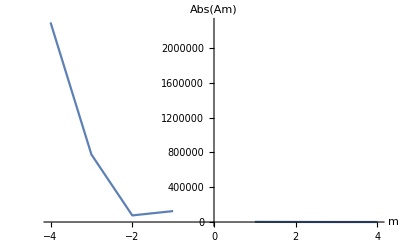

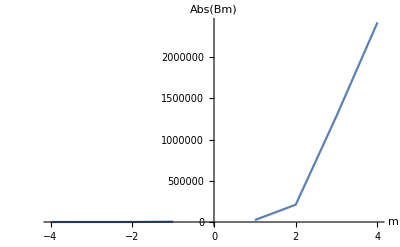

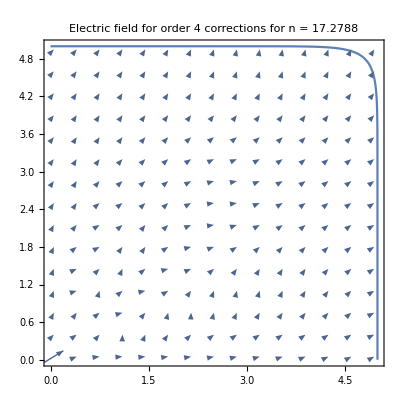

```mathematica
Block[
{M,kMax,m,k,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=4;(* Half the number of coefficients Am or Bm *)
n=N[11π/2];(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia=<||>;Ib=<||>;Ic=<||>;Id=<||>;Ie=<||>;
For[
m=-M,m≤M,m++,
For[
k=1,k≤2M,k++,
Ia=Append[Ia,{m,k}-> NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ib=Append[Ib,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
];
For[
k=0,k≤2M+1,k++,
Ic=Append[Ic,k-> NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Id=Append[Id,{m,k}->NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ie=Append[Ie,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
]
];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[{m,k}]+m B[m]/R^(m+1) Ib[{m,k}],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[{m,k}]+B[m]/R^m Ie[{m,k}],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=Solve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Am)"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Bm)"}]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 2.89229×10^-7-0.000648977 ⅈ and 0.0338104 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 1.79117×10^-6-0.000716219 ⅈ and 0.0433615 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -0.000012216+0.00188805 ⅈ and 0.0362392 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{0.000528033-0.000138691 ⅈ,0.000224583+0.000374998 ⅈ,-0.000895477+0.00233858 ⅈ,0.0403781-0.000799682 ⅈ,0.204461-0.0125242 ⅈ,3.48787×10^-16+4.35984×10^-17 ⅈ,«11»,-0.00300306+0.000242968 ⅈ,-0.00184269+0.000547202 ⅈ,-0.000135721+0.0000450908 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«20»,{«1»}} may contain significant numerical errors.

{{ϕ[0]→-48249.4+15954.4 ⅈ,ϕ[1]→-2.61283×10^16+15.5466 ⅈ,A[-5]→2.86084×10^6+4.9856×10^6 ⅈ,A[-4]→1.21476×10^7-7.52278×10^6 ⅈ,A[-3]→-3.31352×10^6+5.45215×10^6 ⅈ,A[-2]→-151401.-1.08332×10^6 ⅈ,A[-1]→38598.+112473. ⅈ,A[1]→2816.95-7701.67 ⅈ,A[2]→663.726-115.006 ⅈ,A[3]→-137.881+178.911 ⅈ,A[4]→6.9296-27.1148 ⅈ,A[5]→-0.779641+1.67428 ⅈ,B[-5]→0.305494-0.587508 ⅈ,B[-4]→12.9646+6.44188 ⅈ,B[-3]→-62.5284-114.927 ⅈ,B[-2]→-475.753+1606.02 ⅈ,B[-1]→4272.67-691.141 ⅈ,B[1]→52622.9+61857.8 ⅈ,B[2]→100020.+377648. ⅈ,B[3]→-1.72621×10^6-4.71963×10^6 ⅈ,B[4]→1.13119×10^7+1.1605×10^7 ⅈ,B[5]→-1.64916×10^7-3.14442×10^7 ⅈ}}

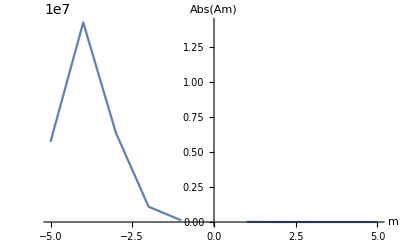

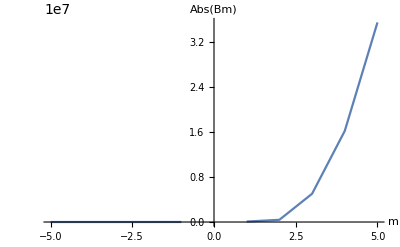

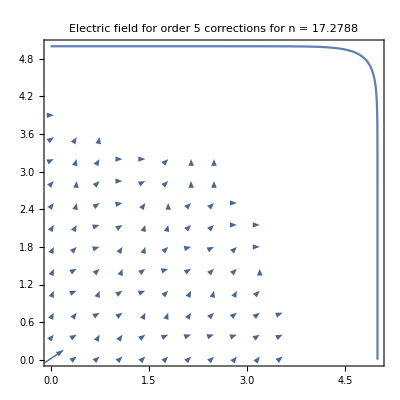

```mathematica
Block[
{M,kMax,m,k,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=5;(* Half the number of coefficients Am or Bm *)
n=N[11π/2];(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia=<||>;Ib=<||>;Ic=<||>;Id=<||>;Ie=<||>;
For[
m=-M,m≤M,m++,
For[
k=1,k≤2M,k++,
Ia=Append[Ia,{m,k}-> NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ib=Append[Ib,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
];
For[
k=0,k≤2M+1,k++,
Ic=Append[Ic,k-> NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Id=Append[Id,{m,k}->NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ie=Append[Ie,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
]
];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[{m,k}]+m B[m]/R^(m+1) Ib[{m,k}],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[{m,k}]+B[m]/R^m Ie[{m,k}],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=Solve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Am)"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Bm)"}]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.00214588+7.81582×10^-6 ⅈ and 0.0252001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 3.81537×10^-6+1.12899×10^-10 ⅈ and 0.0983279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -6.49561×10^-6+0.00110787 ⅈ and 0.0493265 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{0.000089899-0.0000315674 ⅈ,0.000528033-0.000138691 ⅈ,0.000224583+0.000374998 ⅈ,-0.000895477+0.00233858 ⅈ,0.0403781-0.000799682 ⅈ,0.204461-0.0125242 ⅈ,«15»,-0.00184269+0.000547202 ⅈ,-0.000135721+0.0000450908 ⅈ,0.0000533887-0.0000282195 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«24»,{«1»}} may contain significant numerical errors.

{{ϕ[0]→572.113+5547.89 ⅈ,ϕ[1]→-2.61283×10^16-2.22748 ⅈ,A[-6]→2.26856×10^7+1.54815×10^7 ⅈ,A[-5]→-1.13946×10^7-3.27017×10^6 ⅈ,A[-4]→-687556.-2.347×10^6 ⅈ,A[-3]→441043.+1.16533×10^6 ⅈ,A[-2]→-309954.+91999.1 ⅈ,A[-1]→32980.8-46384.7 ⅈ,A[1]→288.414+1102.33 ⅈ,A[2]→98.2351+171.663 ⅈ,A[3]→14.4897-2.46136 ⅈ,A[4]→4.85706+6.40267 ⅈ,A[5]→-0.0999164+1.52634 ⅈ,A[6]→0.0974138-0.129864 ⅈ,B[-6]→0.0313076+0.0992112 ⅈ,B[-5]→-0.696907+0.277335 ⅈ,B[-4]→13.409+4.65981 ⅈ,B[-3]→14.8168-16.8122 ⅈ,B[-2]→128.717-43.2015 ⅈ,B[-1]→465.984+666.534 ⅈ,B[1]→13659.6-16864.7 ⅈ,B[2]→104363.-59665.8 ⅈ,B[3]→407253.+573073. ⅈ,B[4]→-617761.-3.80552×10^6 ⅈ,B[5]→222942.+1.69812×10^7 ⅈ,B[6]→2.23112×10^7-5.32584×10^7 ⅈ}}

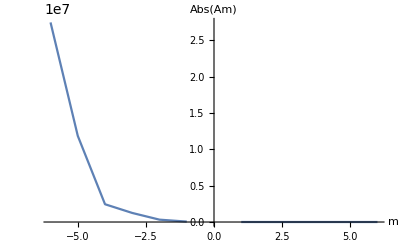

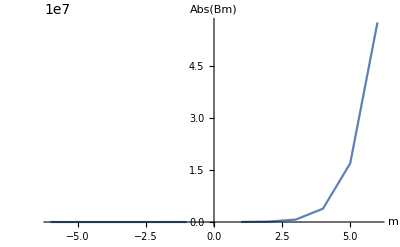

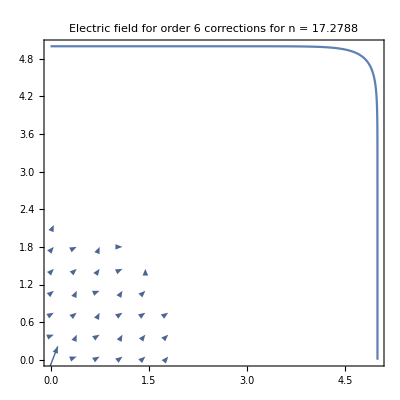

```mathematica
Block[
{M,kMax,m,k,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=6;(* Half the number of coefficients Am or Bm *)
n=N[11π/2];(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia=<||>;Ib=<||>;Ic=<||>;Id=<||>;Ie=<||>;
For[
m=-M,m≤M,m++,
For[
k=1,k≤2M,k++,
Ia=Append[Ia,{m,k}-> NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ib=Append[Ib,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
];
For[
k=0,k≤2M+1,k++,
Ic=Append[Ic,k-> NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Id=Append[Id,{m,k}->NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ie=Append[Ie,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
]
];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[{m,k}]+m B[m]/R^(m+1) Ib[{m,k}],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[{m,k}]+B[m]/R^m Ie[{m,k}],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=Solve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Am)"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Bm)"}]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -4.28029×10^-6+0.000553936 ⅈ and 0.0382398 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.50938}. NIntegrate obtained 8.49545×10^-6-0.000475459 ⅈ and 0.0880489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -0.0000130377+0.00203159 ⅈ and 0.0439371 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-7.23383×10^-6+6.14099×10^-6 ⅈ,0.000089899-0.0000315674 ⅈ,0.000528033-0.000138691 ⅈ,0.000224583+0.000374998 ⅈ,-0.000895477+0.00233858 ⅈ,0.0403781-0.000799682 ⅈ,«19»,-0.000135721+0.0000450908 ⅈ,0.0000533887-0.0000282195 ⅈ,6.08311×10^-6-3.81251×10^-6 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«28»,{«1»}} may contain significant numerical errors.

{{ϕ[0]→-1229.92+12800.3 ⅈ,ϕ[1]→-2.61283×10^16+9.73691 ⅈ,A[-7]→-5.77381×10^8+2.69606×10^8 ⅈ,A[-6]→2.43297×10^7-1.29621×10^8 ⅈ,A[-5]→2.62049×10^7-1.75549×10^7 ⅈ,A[-4]→-1.22133×10^7+1.50707×10^6 ⅈ,A[-3]→1.87333×10^6-3.2707×10^6 ⅈ,A[-2]→-423814.+968988. ⅈ,A[-1]→155818.-276573. ⅈ,A[1]→-516.606+2252.01 ⅈ,A[2]→-957.006-571.819 ⅈ,A[3]→-51.3694-14.8415 ⅈ,A[4]→-13.3198-1.37321 ⅈ,A[5]→2.17678-2.7651 ⅈ,A[6]→0.0293462+0.470375 ⅈ,A[7]→-0.035232-0.0301295 ⅈ,B[-7]→0.0607588+0.0572829 ⅈ,B[-6]→-0.379846-0.662514 ⅈ,B[-5]→2.25868+11.1892 ⅈ,B[-4]→1.39811-2.12311 ⅈ,B[-3]→-73.8296+67.5279 ⅈ,B[-2]→925.34-266.887 ⅈ,B[-1]→-3852.84+4419.24 ⅈ,B[1]→38587.1-29503.7 ⅈ,B[2]→1.21937×10^6-369636. ⅈ,B[3]→-746459.+3.30288×10^6 ⅈ,B[4]→4.28907×10^6-3.04959×10^6 ⅈ,B[5]→1.56627×10^7-2.24313×10^6 ⅈ,B[6]→-1.06647×10^8+6.61931×10^7 ⅈ,B[7]→5.47353×10^8+9.56921×10^7 ⅈ}}

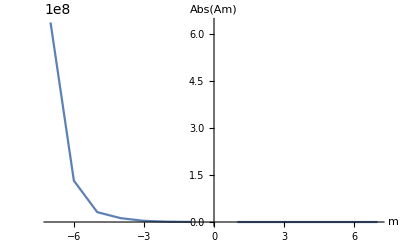

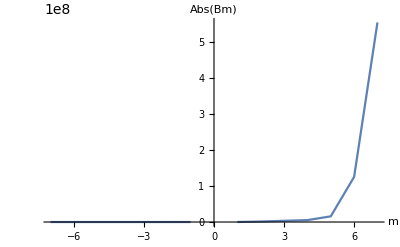

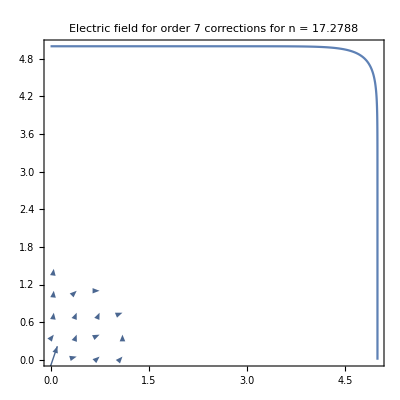

```mathematica
Block[
{M,kMax,m,k,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=7;(* Half the number of coefficients Am or Bm *)
n=N[11π/2];(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia=<||>;Ib=<||>;Ic=<||>;Id=<||>;Ie=<||>;
For[
m=-M,m≤M,m++,
For[
k=1,k≤2M,k++,
Ia=Append[Ia,{m,k}-> NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ib=Append[Ib,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
];
For[
k=0,k≤2M+1,k++,
Ic=Append[Ic,k-> NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Id=Append[Id,{m,k}->NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ie=Append[Ie,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
]
];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[{m,k}]+m B[m]/R^(m+1) Ib[{m,k}],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[{m,k}]+B[m]/R^m Ie[{m,k}],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=Solve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Am)"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Bm)"}]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -5.90043×10^-6+0.000945628 ⅈ and 0.0446243 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained -0.0000108278+0.00335641 ⅈ and 0.133273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.00135989+0.000674964 ⅈ and 0.0270873 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-2.07893×10^-6+1.68384×10^-6 ⅈ,-7.23383×10^-6+6.14099×10^-6 ⅈ,0.000089899-0.0000315674 ⅈ,0.000528033-0.000138691 ⅈ,0.000224583+0.000374998 ⅈ,-0.000895477+0.00233858 ⅈ,«23»,0.0000533887-0.0000282195 ⅈ,6.08311×10^-6-3.81251×10^-6 ⅈ,-2.47214×10^-6+1.58442×10^-6 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«33»} may contain significant numerical errors.

{}

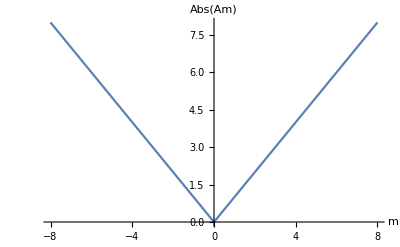

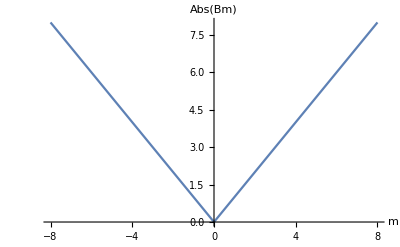

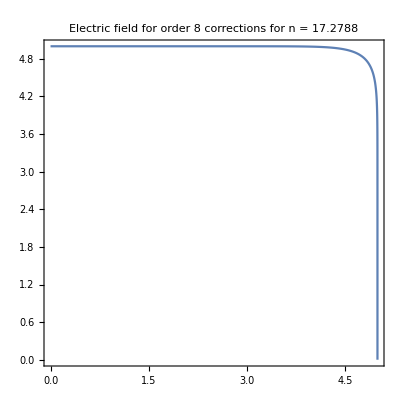

```mathematica
Block[
{M,kMax,m,k,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=8;(* Half the number of coefficients Am or Bm *)
n=N[11π/2];(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia=<||>;Ib=<||>;Ic=<||>;Id=<||>;Ie=<||>;
For[
m=-M,m≤M,m++,
For[
k=1,k≤2M,k++,
Ia=Append[Ia,{m,k}-> NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ib=Append[Ib,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
];
For[
k=0,k≤2M+1,k++,
Ic=Append[Ic,k-> NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Id=Append[Id,{m,k}->NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ie=Append[Ie,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
]
];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[{m,k}]+m B[m]/R^(m+1) Ib[{m,k}],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[{m,k}]+B[m]/R^m Ie[{m,k}],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=Solve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Am)"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Bm)"}]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

{{ϕ[0]→-4.99884×10^-16+2.59026 ⅈ,ϕ[1]→-2.61283×10^16-2.8939×10^-16 ⅈ}}

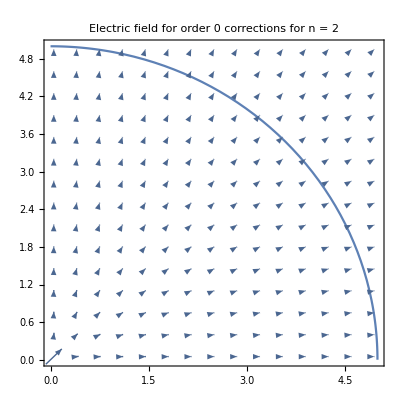

```mathematica
Block[
{M,kMax,m,k,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=0;(* Half the number of coefficients Am or Bm *)
n=2;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia=<||>;Ib=<||>;Ic=<||>;Id=<||>;Ie=<||>;
For[
m=-M,m≤M,m++,
For[
k=1,k≤2M,k++,
Ia=Append[Ia,{m,k}-> NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ib=Append[Ib,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
];
For[
k=0,k≤2M+1,k++,
Ic=Append[Ic,k-> NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Id=Append[Id,{m,k}->NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ie=Append[Ie,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
]
];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[{m,k}]+m B[m]/R^(m+1) Ib[{m,k}],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[{m,k}]+B[m]/R^m Ie[{m,k}],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=Solve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Print[soln];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.50938}. NIntegrate obtained 1.65246×10^-6-0.000629141 ⅈ and 0.00559498 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15318}. NIntegrate obtained -0.00617366+0.571721 ⅈ and 0.0102141 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15318}. NIntegrate obtained -6.28531-0.0275369 ⅈ and 0.0622656 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{ϕ[0]→630.361+373.371 ⅈ,ϕ[1]→-2.61283×10^16+0.550656 ⅈ,A[-1]→88899.7-22811.4 ⅈ,A[1]→-4293.57+995.6 ⅈ,B[-1]→-3757.9+777.206 ⅈ,B[1]→107557.-28168.9 ⅈ}}

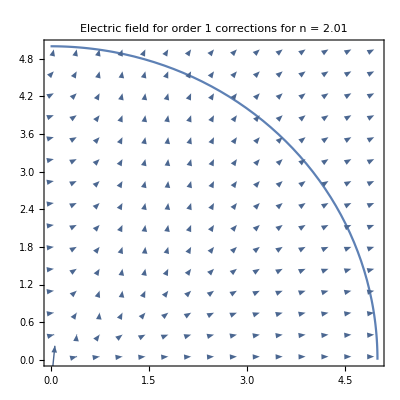

```mathematica
Block[
{M,kMax,m,k,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=1;(* Half the number of coefficients Am or Bm *)
n=2.01;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia=<||>;Ib=<||>;Ic=<||>;Id=<||>;Ie=<||>;
For[
m=-M,m≤M,m++,
For[
k=1,k≤2M,k++,
Ia=Append[Ia,{m,k}-> NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ib=Append[Ib,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
];
For[
k=0,k≤2M+1,k++,
Ic=Append[Ic,k-> NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Id=Append[Id,{m,k}->NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ie=Append[Ie,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
]
];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[{m,k}]+m B[m]/R^(m+1) Ib[{m,k}],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[{m,k}]+B[m]/R^m Ie[{m,k}],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=Solve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Print[soln];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.00275557-0.00270831 ⅈ and 0.03131 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 0.00273077-0.00272009 ⅈ and 0.0311216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.0000116701-0.00191567 ⅈ and 0.0474021 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{ϕ[0]→5632.38+361.125 ⅈ,ϕ[1]→-2.61283×10^16+1.49787 ⅈ,A[-2]→8.44779×10^6-1.54289×10^6 ⅈ,A[-1]→89332.-1.88815×10^6 ⅈ,A[1]→-24187.8+73642.6 ⅈ,A[2]→17507.2+1067.83 ⅈ,B[-2]→-6977.08+10648.4 ⅈ,B[-1]→66278.+122899. ⅈ,B[1]→2.1429×10^6-2.8864×10^6 ⅈ,B[2]→-8.45132×10^6-90804.2 ⅈ}}

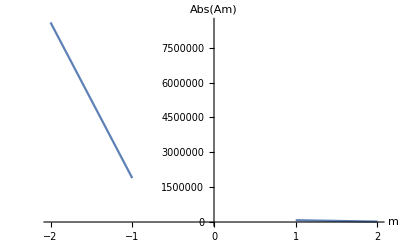

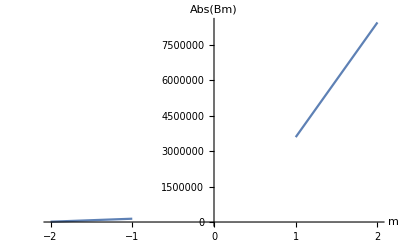

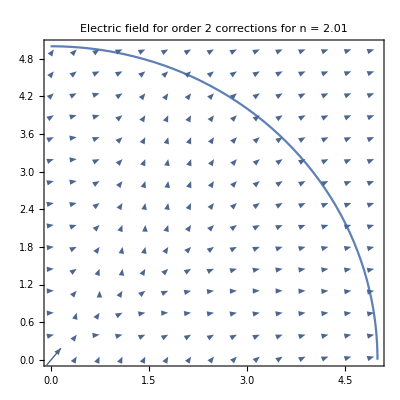

```mathematica
Block[
{M,kMax,m,k,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=2;(* Half the number of coefficients Am or Bm *)
n=2.01;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia=<||>;Ib=<||>;Ic=<||>;Id=<||>;Ie=<||>;
For[
m=-M,m≤M,m++,
For[
k=1,k≤2M,k++,
Ia=Append[Ia,{m,k}-> NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ib=Append[Ib,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
];
For[
k=0,k≤2M+1,k++,
Ic=Append[Ic,k-> NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Id=Append[Id,{m,k}->NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ie=Append[Ie,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
]
];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[{m,k}]+m B[m]/R^(m+1) Ib[{m,k}],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[{m,k}]+B[m]/R^m Ie[{m,k}],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=Solve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Am)"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Bm)"}]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.50938}. NIntegrate obtained 3.18503×10^-6-0.00062604 ⅈ and 0.00929104 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained -1.06886×10^-6-0.000631787 ⅈ and 0.00941162 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.77276}. NIntegrate obtained 1.33316×10^-6-0.000256952 ⅈ and 0.0130672 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{ϕ[0]→1168.19+4638.12 ⅈ,ϕ[1]→-2.61283×10^16+2.80234 ⅈ,A[-3]→-1.05058×10^7-2.35851×10^7 ⅈ,A[-2]→124490.+1.94074×10^6 ⅈ,A[-1]→143161.+64983.7 ⅈ,A[1]→23685.2-33008. ⅈ,A[2]→1316.22-125.853 ⅈ,A[3]→-434.597+17.5427 ⅈ,B[-3]→452.455+1268.51 ⅈ,B[-2]→-1690.45-7366.45 ⅈ,B[-1]→-194.723-28208.2 ⅈ,B[1]→-214821.+1.37159×10^6 ⅈ,B[2]→-307514.-1.15659×10^6 ⅈ,B[3]→-1.96729×10^6+4.75611×10^6 ⅈ}}

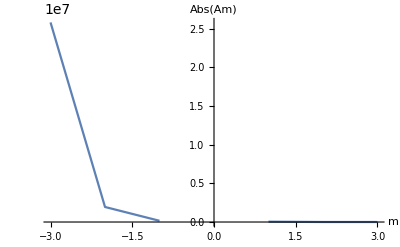

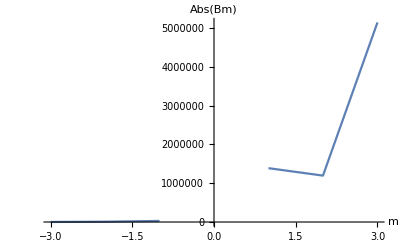

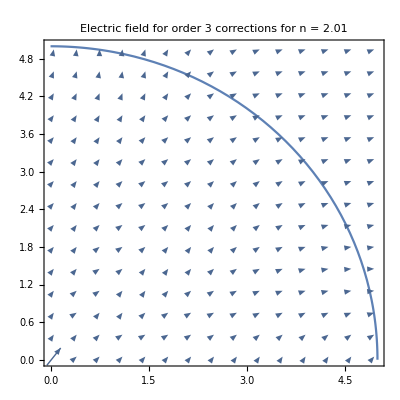

```mathematica
Block[
{M,kMax,m,k,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=3;(* Half the number of coefficients Am or Bm *)
n=2.01;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia=<||>;Ib=<||>;Ic=<||>;Id=<||>;Ie=<||>;
For[
m=-M,m≤M,m++,
For[
k=1,k≤2M,k++,
Ia=Append[Ia,{m,k}-> NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ib=Append[Ib,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
];
For[
k=0,k≤2M+1,k++,
Ic=Append[Ic,k-> NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Id=Append[Id,{m,k}->NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ie=Append[Ie,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
]
];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[{m,k}]+m B[m]/R^(m+1) Ib[{m,k}],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[{m,k}]+B[m]/R^m Ie[{m,k}],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=Solve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Am)"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Bm)"}]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -4.71845×10^-16-1.64056×10^-15 ⅈ and 3.21318×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.1415}. NIntegrate obtained -5.82867×10^-16+6.0077×10^-16 ⅈ and 1.46474×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.5707}. NIntegrate obtained -1.24038×10^-15-5.55112×10^-17 ⅈ and 9.0857×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-1.17684×10^-17-4.70885×10^-17 ⅈ,0.219968+0. ⅈ,7.77156×10^-16+1.73472×10^-17 ⅈ,5.82867×10^-15-6.0077×10^-15 ⅈ,-7.63278×10^-15+6.58207×10^-15 ⅈ,6.28319+0. ⅈ,2.44249×10^-17-1.02×10^-17 ⅈ,7.54952×10^-18+2.6249×10^-17 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«8»,{-1.72085×10^-17-4.27734×10^-17 ⅈ,«9»,-3.12459-«20» ⅈ}} may contain significant numerical errors.

{}

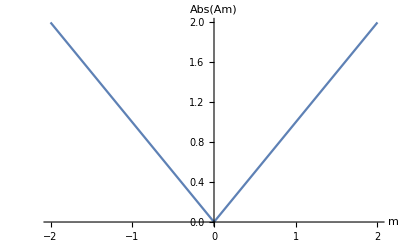

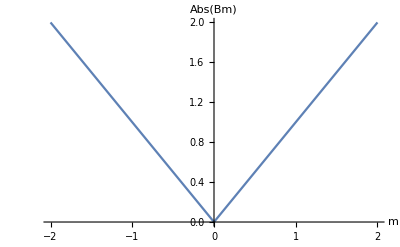

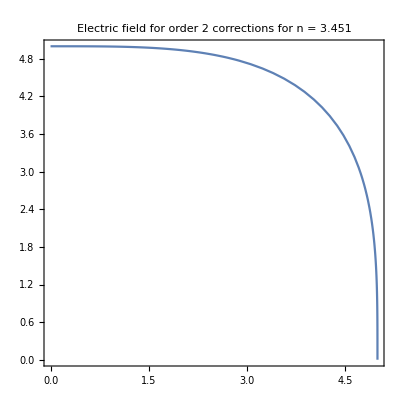

```mathematica
Block[
{func,M,kMax,m,k,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=2;(* Half the number of coefficients Am or Bm *)
n=3.451;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia=<||>;Ib=<||>;Ic=<||>;Id=<||>;Ie=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
m=-M,m≤M,m++,
For[
k=1,k≤2M,k++,
Ia=Append[Ia,{m,k}-> NIntegrate[Exp[I(m-k) θ]/(func[θ,n]^(m-1)),{θ,0,2π}]];
Ib=Append[Ib,{m,k}-> NIntegrate[Exp[I(m-k) θ](func[θ,n]^(m+1)),{θ,0,2π}]];
];
For[
k=0,k≤2M+1,k++,
Ic=Append[Ic,k-> NIntegrate[Log[func[θ,n]]Exp[-I k θ],{θ,0,2π}]];
Id=Append[Id,{m,k}->NIntegrate[Exp[I(m-k) θ]/(func[θ,n]^(m)),{θ,0,2π}]];
Ie=Append[Ie,{m,k}-> NIntegrate[Exp[I(m-k) θ]func[θ,n]^m,{θ,0,2π}]];
]
];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[{m,k}]+m B[m]/R^(m+1) Ib[{m,k}],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[{m,k}]+B[m]/R^m Ie[{m,k}],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=Solve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Am)"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Bm)"}]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```